```mathematica
a=Table[x Pi 5/ 16,{x,0,1,1/400}];
```

```mathematica
b =Table[x,{x,0,1,1/400}];
```

```mathematica
c = Join[a,b];
```

```mathematica
f[x_]=Which[Element[x,Rationals],Denominator[x],Not[Element[x,Rationals]],0];
```

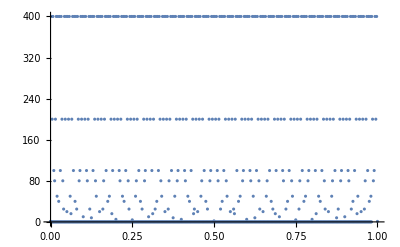

```mathematica
ListPlot[Table[{x,f[x]},{x,c}]]
```

```mathematica
Table[{x,f[x]},{x,c}]
```

{{0,1},{π^2/50,0},{π^2/25,0},{(3 π^2)/50,0},{(2 π^2)/25,0},{π^2/10,0},{(3 π^2)/25,0},{(7 π^2)/50,0},{(4 π^2)/25,0},{(9 π^2)/50,0},{π^2/5,0},{(11 π^2)/50,0},{(6 π^2)/25,0},{(13 π^2)/50,0},{(7 π^2)/25,0},{(3 π^2)/10,0},{(8 π^2)/25,0},{(17 π^2)/50,0},{(9 π^2)/25,0},{(19 π^2)/50,0},{(2 π^2)/5,0},{(21 π^2)/50,0},{(11 π^2)/25,0},{(23 π^2)/50,0},{(12 π^2)/25,0},{π^2/2,0},{(13 π^2)/25,0},{(27 π^2)/50,0},{(14 π^2)/25,0},{(29 π^2)/50,0},{(3 π^2)/5,0},{(31 π^2)/50,0},{(16 π^2)/25,0},{(33 π^2)/50,0},{(17 π^2)/25,0},{(7 π^2)/10,0},{(18 π^2)/25,0},{(37 π^2)/50,0},{(19 π^2)/25,0},{(39 π^2)/50,0},{(4 π^2)/5,0},{(41 π^2)/50,0},{(21 π^2)/25,0},{(43 π^2)/50,0},{(22 π^2)/25,0},{(9 π^2)/10,0},{(23 π^2)/25,0},{(47 π^2)/50,0},{(24 π^2)/25,0},{(49 π^2)/50,0},{π^2,0},{0,1},{1/50,50},{1/25,25},{3/50,50},{2/25,25},{1/10,10},{3/25,25},{7/50,50},{4/25,25},{9/50,50},{1/5,5},{11/50,50},{6/25,25},{13/50,50},{7/25,25},{3/10,10},{8/25,25},{17/50,50},{9/25,25},{19/50,50},{2/5,5},{21/50,50},{11/25,25},{23/50,50},{12/25,25},{1/2,2},{13/25,25},{27/50,50},{14/25,25},{29/50,50},{3/5,5},{31/50,50},{16/25,25},{33/50,50},{17/25,25},{7/10,10},{18/25,25},{37/50,50},{19/25,25},{39/50,50},{4/5,5},{41/50,50},{21/25,25},{43/50,50},{22/25,25},{9/10,10},{23/25,25},{47/50,50},{24/25,25},{49/50,50},{1,1}}